```mathematica
SetOptions[ListLinePlot, ImageSize->800, Frame -> True, Axes->False];
```

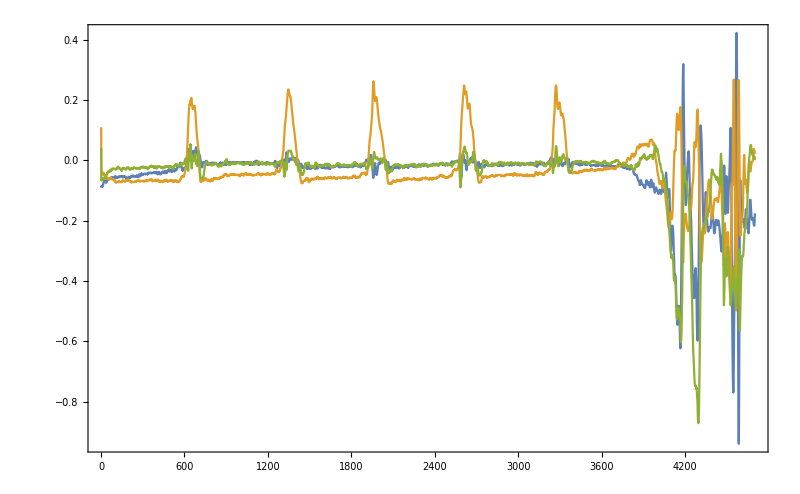

```mathematica
data = Drop[Import["/home/nils/Projects/C/Handschuh/USB/driver/output.dat", "Table"], -1];
ListLinePlot[{data[[All, 1]], data[[All, 2]], data[[All, 3]]}, PlotRange->Full]
```

```mathematica
GetParameters[dataPiece_/;Length[dataPiece] ≠ 200] := Missing[]
GetParameters[dataPiece_/;Length[dataPiece] == 200] := Block[{
max = Flatten[MaximalBy[#, Identity, 1]& /@ {dataPiece[[All,1]], dataPiece[[All, 2]], dataPiece[[All, 3]]}], min = Flatten[MinimalBy[#, Identity, 1]& /@ {dataPiece[[All,1]], dataPiece[[All, 2]], dataPiece[[All, 3]]}]},
{
"StartValue" -> dataPiece[[1]],
"EndValue" -> dataPiece[[-1]],
"MaxValue" -> max,
"MinValue" -> min,
"Length" -> (Function[i,Length[Select[dataPiece[[All, i]], min[[i]] < # < max[[i]]&]]] /@ {1,2,3})
}]
dataClassify = Table[GetParameters[data[[i;;i+199]]] ,{i,1,900,1}];
```

```mathematica
Classifier[i_/; 539 ≤ i ≤ 600] := Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /. dataClassify[[i]]] -> "A"
Classifier[i_] := Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /. dataClassify[[i]]] -> "0"
dataClassifyClassified = Table[Classifier[i], {i,1,Length[dataClassify]}];
Classified = Classify[dataClassifyClassified];
```

```mathematica
Solution = Table[
Flatten[{"StartValue", "EndValue", "MaxValue", "MinValue", "Length"} /.GetParameters[data[[i;;i+199]]]],
{i,1,Length[data] - 200,1}];
```

$Aborted

```mathematica
GraphicsRow[Solution/. {"A" -> Graphics[{Red, Rectangle[]}], "0" -> Graphics[{Black, Rectangle[]}]}]
```

$Aborted[]